#### Input

```mathematica
targetSymbol=Sin[x];
range={-7, 7, 0.05};
```

#### Function and Constants Initialization

```mathematica
toFunc[symb_, var_:x][dontusethisvariable_]:=With[{symb2=symb/.var->dontusethissymbol}, symb2/.{dontusethissymbol->dontusethisvariable}]
funcFromVals[xVals_,vals_][x_]:=Quiet[Interpolation[Transpose[{xVals, vals}],InterpolationOrder->1][x], {InterpolatingFunction::dmval, InterpolatingFunction::dprec}]
funcFromVals[xVals_,vals_, extrapolatingFunc_][x_]:=If[x<Min[xVals],extrapolatingFunc[x],If[x>Max[xVals],extrapolatingFunc[x],Quiet[Interpolation[Transpose[{xVals, vals}],InterpolationOrder->1][x], InterpolatingFunction::dprec]]]
```

```mathematica
target=toFunc[targetSymbol];
pRange=AbsoluteOptions[Plot[target[x], {x, range[[1]], range[[2]]}, ImageSize->Medium],PlotRange][[1,2]];
PlotFunc[func_]:=Plot[func[x], {x, range[[1]], range[[2]]}, PlotRange->pRange]
PlotVals[vals_, xVals_, prange_:pRange]:=Show[{ListPlot[Transpose[{xVals, vals}], PlotRange-> prange], PlotFunc[funcFromVals[xVals, vals]]}]
```

#### Approximation Initialization

```mathematica
(* Find a fixed point of the target, as it gives one point which is definitly on the graph of the functional iterate. *)fixedPoint=x/.Last[NMinimize[{(x-targetSymbol)^2, x∈Interval[range[[1;;2]]]}, x,PrecisionGoal->50]];
fixedPoint=If[Mod[fixedPoint, 1]<=10^-20, Floor[fixedPoint], fixedPoint] (* Rounding, if necesary *)

(* First two terms of Maclaurin series to make a linear approximation around x = fixedPoint *)
twoMaclaurinTerms={targetSymbol/.x->fixedPoint, D[targetSymbol, x]/.x->fixedPoint};

(* y = term[[1]]+term[[2]](x - fixedPoint) -> y = (term[[1]] - term[[2]]fixedPoint) + term[[2]]x *)
twoMaclaurinTerms={twoMaclaurinTerms[[1]] - twoMaclaurinTerms[[2]]*fixedPoint, twoMaclaurinTerms[[2]]};

(* Half-Iterate of Maxlaurin Terms (can be complex sometimes) *)
approxSymbol=N[twoMaclaurinTerms[[1]]/(1+√twoMaclaurinTerms[[2]])+√twoMaclaurinTerms[[2]] x] 
originalApproxFunc=toFunc[approxSymbol];
approxFunc=toFunc[approxSymbol];
nestedApproxFunc:=approxFunc[approxFunc[#]]&;
```

0

x

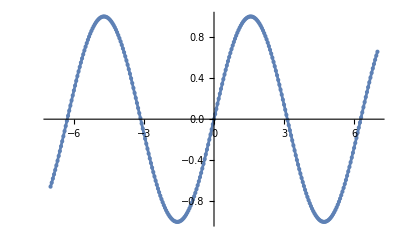

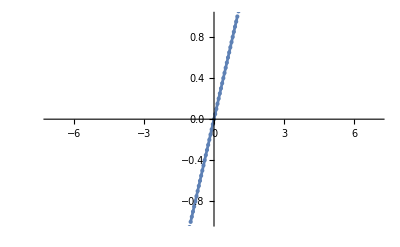

```mathematica
PlotVals[target/@(Range@@range), (Range@@range)]
PlotVals[nestedApproxFunc/@(Range@@range), (Range@@range)]
```

#### Base Values

```mathematica
xVals={fixedPoint}
plots={};

updatenxVals[]:=nxVals=Union[xVals, Clip[#, range[[1;;2]]]&/@{Min[xVals]-range[[3]],Max[xVals]+range[[3]]}];
updatenxVals[]
```

{0}

{-0.05,0,0.05}

#### Running Through Manually

```mathematica
approxVals=approxFunc/@nxVals
nestedApproxVals=nestedApproxFunc/@nxVals
deltaVals=(target/@nxVals)-nestedApproxVals
e=Plus@@(deltaVals^2)
deltaVals=deltaVals*Table[If[i==1||i==Length[deltaVals], 1, 0], {i, Length[deltaVals]}]
newApproxVals=(approxVals+0.5*deltaVals)
approxFunc=funcFromVals[nxVals, newApproxVals,originalApproxFunc]
```

{-0.199333,-0.0999167,0.,0.0999167,0.199333}

{-0.198669,-0.0998334,0.,0.0998334,0.198669}

{0.,0.,0.,1.38778×10^-17,0.}

1.92593×10^-34

{0.,0.,0.,0.,0.}

{-0.199333,-0.0999167,0.,0.0999167,0.199333}

funcFromVals[{-0.2,-0.1,0,0.1,0.2},{-0.199333,-0.0999167,0.,0.0999167,0.199333},toFunc[x]]

0.0000173581

{-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3}

{-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4}

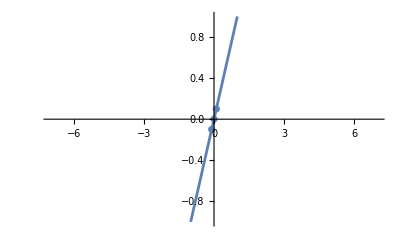
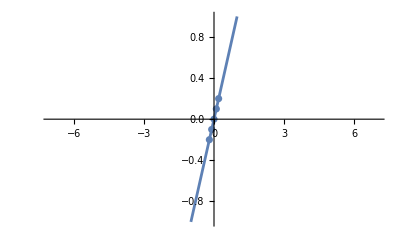
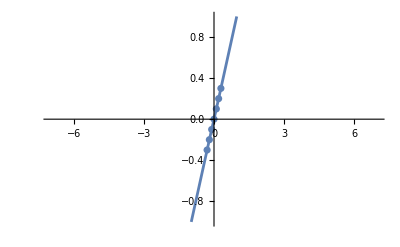
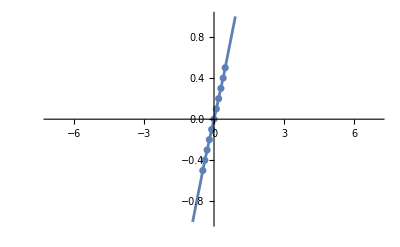
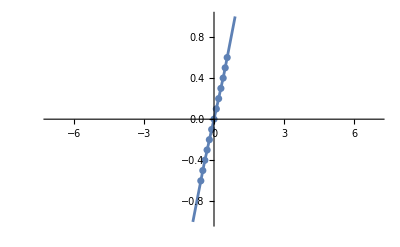
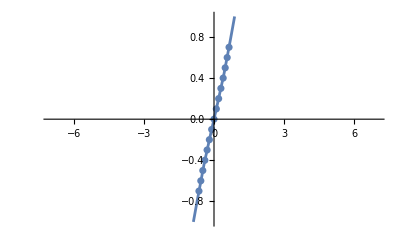
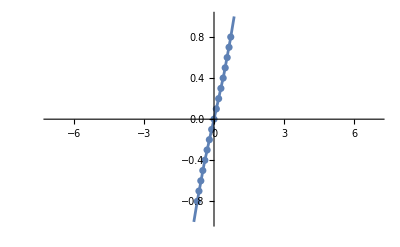
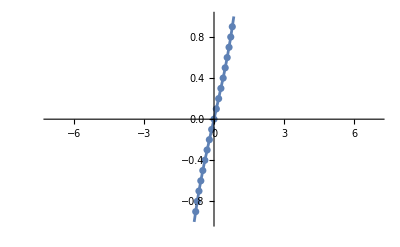
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FixedPoint[updateApproxVals, 0.]
plots=AppendTo[plots, PlotVals[nxVals, nestedApproxVals]];
xVals=nxVals
updatenxVals[]
plots
```

#### Running Through Automatically

```mathematica
updateApproxVals[nothing_]:=Module[{},
approxVals=approxFunc/@nxVals;
nestedApproxVals=nestedApproxFunc/@nxVals;
deltaVals=(target/@nxVals)-nestedApproxVals;
e=Plus@@(deltaVals^2);
deltaVals=deltaVals*Table[If[i==1||i==Length[deltaVals], 1, 0], {i, Length[deltaVals]}];
newApproxVals=(approxVals+0.5*deltaVals);
approxFunc=funcFromVals[nxVals, newApproxVals];
e]
```

```mathematica
updateApproxValsOPTIMIZED[nothing_]:=Module[{},
approxVals=approxFunc/@nxVals;
nestedApproxVals=nestedApproxFunc/@nxVals;
deltaVals=(target/@{First[nxVals], Last[nxVals]})-{First[nestedApproxVals],Last[nestedApproxVals]};
e=Plus@@(deltaVals^2);
newApproxVals=approxVals;
newApproxVals[[1]]=newApproxVals[[1]]+0.5*deltaVals[[1]];
newApproxVals[[Length[newApproxVals]]]=newApproxVals[[Length[newApproxVals]]]+0.5*deltaVals[[2]];
approxFunc=funcFromVals[nxVals, newApproxVals];
e]
```

RUN THIS:

```mathematica
While[xVals!=nxVals,
p1=FixedPoint[updateApproxValsOPTIMIZED, 0.];
AppendTo[plots, PlotVals[nxVals, nestedApproxVals, Automatic]];

xVals=nxVals;
p2=SymmetricDifference[updatenxVals[], xVals];

NotebookDelete[progress];
progress=PrintTemporary[{p1,p2,Last[plots]}];
];
```

#### Output

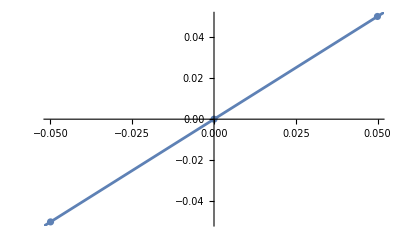
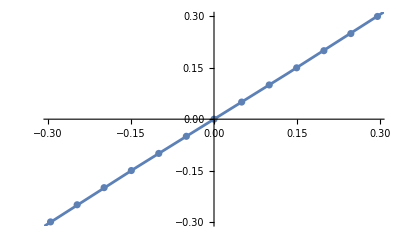
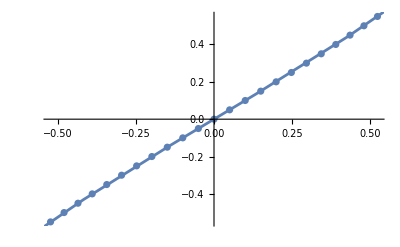
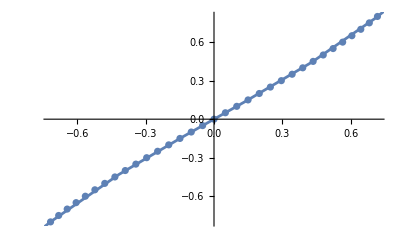
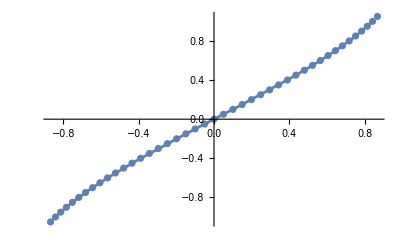
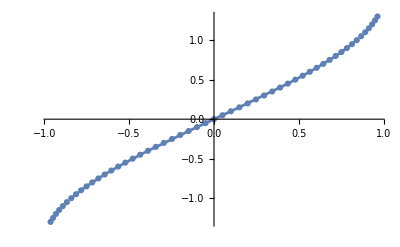
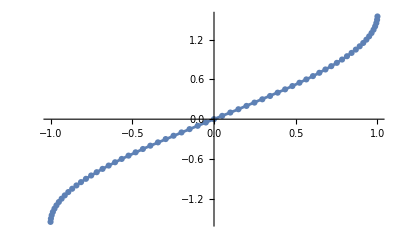
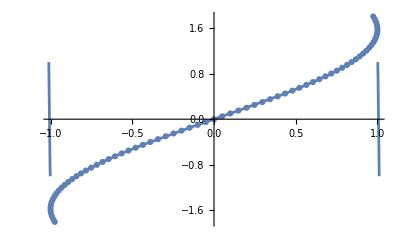

```mathematica
plots[[Range[1, Length[plots], 5]]]
```

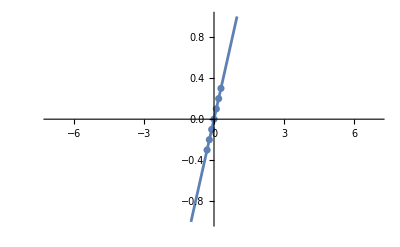

-Graphics-

```mathematica
PlotVals[nxVals, approxVals]
PlotVals[nxVals, nestedApproxVals]
```